# An Overview of the Universe

From elementary particles to the cosmic microwave background.

Andréia Ribeiro de Noronha Sales, Jun. 27,  2018

The universe has been a tremendous source of fascination and exploration for millennia and understanding its inner workings and its history has always required the combined efforts of many people over time. Luckily, the power of computation makes it easier for us to visualize the broadness and beauty of the cosmos.

## The Cosmos in Small Scales

It was once believed that the atom was the smallest unit of matter. Today, we have detected many subatomic particles and predicted the existence of many others. We can ask the Wolfram Language about the elementary particles it knows about.

Get number of elementary particles in the database:

```mathematica
Length[ParticleData[]]
```

1002

Get known properties of particles:

```mathematica
ParticleData["Properties"]
```

{Antiparticle,BaryonNumber,Bottomness,Charge,ChargeStates,Charm,CParity,DecayModes,DecayType,Excitations,FullDecayModes,FullSymbol,GenericFullSymbol,GenericSymbol,GFactor,GParity,HalfLife,Hypercharge,Isospin,IsospinMultiplet,IsospinProjection,LeptonNumber,Lifetime,Mass,MeanSquareChargeRadius,Memberships,Parity,PDGNumber,QuarkContent,Spin,Strangeness,Symbol,Topness,UnobservedDecayModes,Width}

Now let’s dive inside the atom and get a sense for the size of the small cosmos!

Check for proton and neutron components:

```mathematica
ParticleData["Proton","QuarkContent"]
```

{{d,u,u}}

```mathematica
ParticleData["Neutron","QuarkContent"]
```

{{d,d,u}}

Get mass of different particles:

```mathematica
particles = Join[ParticleData["Lepton","Mass"],ParticleData["Hadron","Mass"],ParticleData["Boson","Mass"],ParticleData["Quark","Mass"]]//Sort;
```

Plot the mass distribution of elementary particles in units of MeV/c^2:

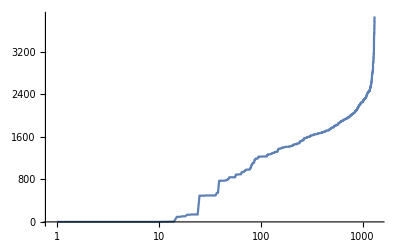

```mathematica
ListLogLinearPlot[particles,Joined-> True]
```

## Solar System Scales

Jumping from the inside of an atom straight to planetary systems and stars seems like a huge leap. And it is! But even the Solar System is tiny when compared to the large scale structure of the universe. So let’s explore our neighborhood a little bit.

First, we set the mood for exploration by looking at some pictures:

```mathematica
PlanetData[PlanetData[],"Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
StarData["Sun","Image"]
```

-Graphics-

Now let’s get a sense for the size of the Solar System. We have more data to work with here. We can get a better idea of the scales involved by plotting the parameters for mass and radius distributions.

Get mass and radius of planets:

```mathematica
mass = PlanetData[PlanetData[],"Mass"]//Sort;
```

```mathematica
radius = PlanetData[PlanetData[],"Radius"]//Sort;
```

Mass distribution:

```mathematica
ListLogPlot[mass, Joined-> True];
```

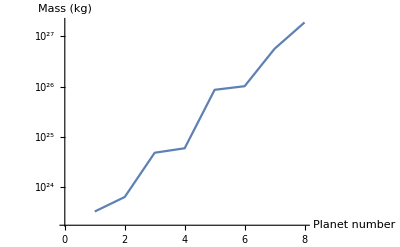

```mathematica
Show[%78,AxesLabel->{HoldForm["Planet number"],HoldForm["Mass (kg)"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Radius distribution:

```mathematica
ListLogPlot[radius, Joined -> True];
```

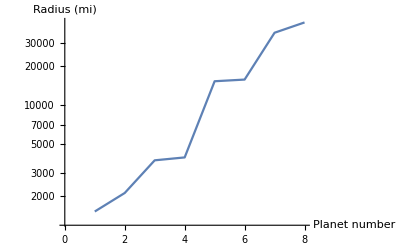

```mathematica
Show[%101,AxesLabel->{HoldForm["Planet number"],HoldForm["Radius (mi)"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Now let’s see what happens when we add the Sun’s mass and radius to the list! It is easier to understand how much bigger and massive the Sun is in comparison to the planets when we visualize it.

Get Sun's data:

```mathematica
solarmass = StarData["Sun", "Mass"];
sunradius = StarData["Sun","Radius"];
```

Add data to original lists:

```mathematica
totalmass= Append[mass, solarmass];
totalradius= Append[radius, sunradius];
```

Plot both parameters again:

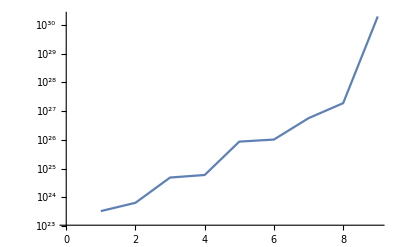

```mathematica
ListLogPlot[totalmass,Joined->True]
```

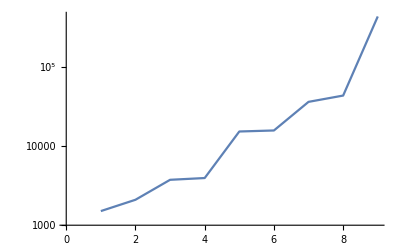

```mathematica
ListLogPlot[totalradius,Joined->True]
```

## The Cosmos in Large Scales

Now we are ready to explore the vastness of the universe in large scales. To do so, let’s first analyze how the universe evolved through the different epochs.

Manipulate powers of 10 to see what parameter dominated during each epoch:

```mathematica
Manipulate[UniverseModelData[Quantity[10^time,"Years"],"Epoch"],{time,1,11,1},SaveDefinitions->True]
```

Manipulate powers of 10 to see how the volume of the universe expanded over time:

```mathematica
Manipulate[UniverseModelData[Quantity[10^t, "LightYears"],"ComovingVolume"],{t,1,10,1},SaveDefinitions->True]
```

Watch the temperature of radiation in the universe evolve over time:

```mathematica
Manipulate[UniverseModelData[Quantity[10^t,"Years"],"RadiationTemperature"],{t,6,11,0.2},SaveDefinitions->True]
```

The farthest back in time we can see is the Cosmic Microwave Background. Let’s take a look!

Find pictures online:

```mathematica
WebImageSearch["CosmicMicrowaveBackground","Thumbnails","MaxItems"-> 2]
```

{-Graphics-,-Graphics-}

## Further explorations

There is a lot of the universe that can be explored in the Wolfram Language. This essay was an overview of a few of the different possibilities. In the future, it would be interesting to explore the available data more deeply and see how much of the cosmos can be understood and visualized.

## Author contact information

andreia.ribeiro@colorado.edu